## Луд А. С. Лабораторная работа №7 : Статистический анализ в системе Mathematica

## Задание 1: Элементарная описательная статистика

```mathematica
data=RandomReal[{20,40},8](*8 случайных вещественных чисел от 20 до 40*)
```

{24.0261,35.2452,22.5189,28.6866,38.7667,21.2162,32.1345,35.4499}

```mathematica
Mean[data] (*Находит среднее значение*)
```

29.7555

```mathematica
Median[data](*Находит значение середины*)
```

30.4105

```mathematica
Max[data](*Находит максимальное значение*)
```

38.7667

```mathematica
Variance[data](*Находит дисперсию*)
```

44.0975

```mathematica
StandardDeviation[data](*Находит среднеквадратичное отклонение*)
```

6.6406

```mathematica
Quantile[data,1/2](*Находит квантитиль*)
```

28.6866

```mathematica
Quartiles[data](*Находит квантитили для списка*)
```

{23.2725,30.4105,35.3475}

## Задание 2: Работа со статистическими распределениями

```mathematica
PDF[NormalDistribution[μ,σ],x] (*дает функцию плотности вероятности для распределения, оцененного в точке x*)
PDF[NormalDistribution[1,3],3]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

1/(3 ⅇ^(2/9) √(2 π))

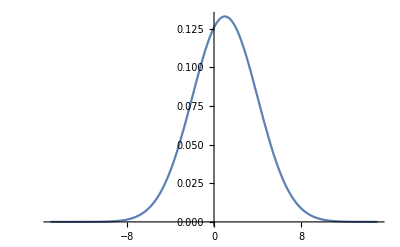

```mathematica
Plot[PDF[NormalDistribution[1,3],x],{x,-15,15}]
```

```mathematica
CharacteristicFunction[NormalDistribution[μ,σ],t] (*дает характеристическую функцию для распределения в зависимости от переменной t*)
CharacteristicFunction[CauchyDistribution[μ,σ],t]  (*распределени коши*)
```

ⅇ^(ⅈ t μ-(t^2 σ^2)/2)

ⅇ^(ⅈ t μ-t σ Sign[t])

```mathematica
(*дает среднее значение успеха в 1000 независимых 
испытаниях, где вероятность успеха в каждом испытании равна 0.1*)
Mean[BinomialDistribution[1000,.1]]
```

100.

```mathematica
Moment[PoissonDistribution[μ],n](*дает n-й момент выборки элементов в списке*)
```

Piecewise[{{BellB[n,μ], n≥0}, {0, True}}]

```mathematica
(*дает псевдослучайную переменную из символического распределения dist.*)
RandomVariate[GeometricDistribution[1/3],20]
```

{1,0,7,0,9,1,3,2,0,5,6,6,4,1,0,0,0,0,0,2}

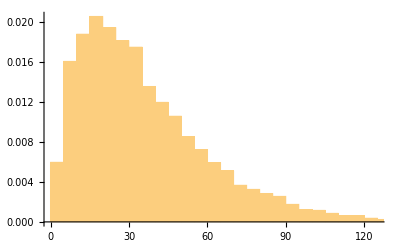

```mathematica
data=RandomVariate[GammaDistribution[2,18],10000];
hist=Histogram[data,Automatic,"ProbabilityDensity"]
```

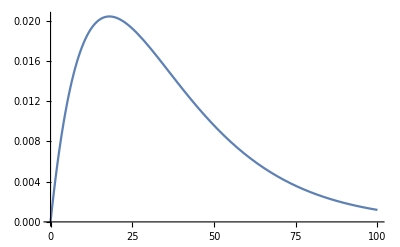

```mathematica
pl=Plot[PDF[GammaDistribution[2,18],x],{x,0,100}]
```

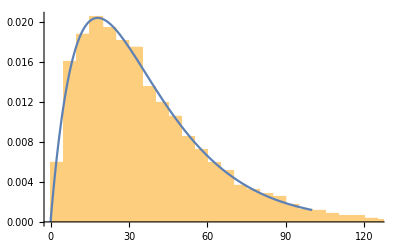

```mathematica
Show[hist,pl]
```

## Задача: Температура 2-х городов

```mathematica
dat1=WeatherData["Tokyo", "MeanTemperature",{{2019,1,1},{2021,12,31},"Day"},"Value"];
dat2=WeatherData["Paris", "MeanTemperature",{{2019,1,1},{2021,12,31},"Day"},"Value"];
PairedHistogram[dat1,dat2,{1},ChartStyle->{{Green,Purple},None},
ChartLabels->Placed[{"Tokyo","Paris"},Above],ImageSize->600,
BaseStyle->{FontFamily->"Consolas",FontSize->16},
PlotLabel->"Средняя температура в цельсиях январь 2019 - январь 2022" ]
```

-Graphics-

## Задача: Кластеризация среза черепа

```mathematica
ClusteringComponents[-Graphics-,7]//Colorize
```

-Graphics-